```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Clear["Global`*"];
guardarSesion[]:=Block[{},
Save["numeroCajaAux.mx", numeroCajaAux];
Save["cajaNumero.mx", cajaNumero];
Save["OutputVSPODEAux.mx",  OutputVSPODEAux];
];
```

```mathematica
cargarBackup[]:=Block[{},
 <<"numeroCajaAux.mx";
 <<"cajaNumero.mx";
 <<"valorFuncionIntHash.mx";
 <<"OutputVSPODEAux.mx";
];
```

Definitions for coloring plots:

```mathematica
color1 = RGBColor[.94,0.93,.96];
color2 = RGBColor[.74,.74,.86];
color3 = RGBColor[.46,.42,.69];
color4 = RGBColor[.53,.34,.65];
ColorSetter [#] & /@{color1, color2, color3,color4}
```

```mathematica
curvasuperior = color4;
curvainferior = color3;
```

## Definition of some values in interval arithmetic

```mathematica
$MinPrecision=4;
$MaxPrecision=10;
$Rounded = 0.000001;
```

```mathematica
(*$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>(
s<>"`10.")&);*)
```

```mathematica
Clear[keys];
keys[l_]:=DownValues[l, Sort-> False][[All,1,1,1]]
```

```mathematica
Clear[fromInterval];
fromIntervalInternal[{a_, b_}] :=SetPrecision[{Round[a,$Rounded],Round[b, $Rounded]}, $MaxPrecision];
fromIntervalInternal[Interval[{a_, b_}]] :=fromIntervalInternal[{a,b}];
fromInterval[x_]:=ReplaceAll[x , caja_Interval :> fromIntervalInternal[caja]] 

toInterval[Interval[{a_,b_}]] := SetPrecision[Interval[{Round[a, $Rounded],Round[b, $Rounded]}], $MaxPrecision];
toInterval[{a_,b_}]:= toInterval[Interval[{a,b}]]
toInterval[{t_, a_, b_}]:=toInterval[Interval[{a,b}]]
toInterval[a_]:=toInterval[Interval[a]]
```

### Define Midpoint and Radius function for interval data:

```mathematica
MidIntervalData[Interval[{L_,U_}]] := (L+U)/2; (*Midpoint definition*)
RadiusIntervalData[Interval[{L_,U_}]]:= (U-L)/2; (*radius of an interval definition. Upper bound minus Midpoint*)
```

### Definiendo la distancia entre intervalos

d(X,Y) = max_{1≤ i≤ n}{|X_Li-Y_Li |,|X_i^U - Y_i^U |}

```mathematica
IntervalDistance[Interval[{xl_,xu_}],Interval[{yl_,yu_}]]:= Max[{Abs[xl-yl],Abs[xu-yu]}] 

VectorialDistance[X_List,Y_List]:= 
	Sum[ IntervalDistance[X[[i]], Y[[i]]]
	, {i, 1, 4}]
```

## Forward Problem VSPODE

```mathematica
SetEnvironment["PATH"-> "/usr/bin:/bin:/usr/sbin:/sbin:/usr/local/bin"];
```

```mathematica
VerificationTest[RunProcess[{"g++-10", "--version"}],
<|"ExitCode"->0,"StandardOutput"->"g++-10 (Homebrew GCC 10.2.0) 10.2.0\nCopyright (C) 2020 Free Software Foundation, Inc.\nThis is free software; see the source for copying conditions.  There is NO\nwarranty; not even for MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.\n\n","StandardError"->""|>];
```

```mathematica
SetDirectory[NotebookDirectory[]];

Clear[VSPODE];
VSPODE[ZZ_List, Model_, params_,removeFiles_:True]:= Module[
	{templateCPP, modelCPP, templateH, modelH, process,output, nameModel, runAns,Z},
	Z = fromInterval[ZZ];
	SetDirectory[NotebookDirectory[]];
	SetEnvironment["PATH"-> "/usr/bin:/bin:/usr/sbin:/sbin:/usr/local/bin"];
	$SystemShell="/bin/zsh";
	$currentBox = Z;

	templateH = FileTemplate[FileNameJoin[{"templates","template.h"}]];
    modelH = TemplateApply[templateH, <| "model" -> Model |>];
    nameModel = ToUpperCase@Model[[1,2]];
    
	$msg = "Creando archivos VSPODE c++..";
    Export[nameModel<>".h", modelH, "Text"];
    Export[nameModel<>"aux1.cpp", TemplateApply[FileTemplate[FileNameJoin[{"templates","templateaux1.cpp"}]], <| "model" -> Model |> ], "Text"];
    Export[nameModel<>"aux2.cpp", TemplateApply[FileTemplate[FileNameJoin[{"templates","templateaux2.cpp"}]], <| "model" -> Model |> ], "Text"];
   
    templateCPP = FileTemplate[FileNameJoin[{"templates","template.cpp"}]];
    modelCPP = TemplateApply[templateCPP, 
     Join[<|"Z" -> Z(*interval for uncertain quantities.
				The first (m-p) quantities are initial value
				the last p quantities are parameters*)
          |>, params]
      , InsertionFunction->ToString
    ];
    Export[nameModel<>".cpp",modelCPP, "Text"];

    runAns = Check[
		RunProcess[{"g++-10", "-O", "-I.././include/", "-I../FADBAD++/.", "-o", nameModel
       , nameModel<>".cpp"
       , nameModel<>"aux1.cpp"
       , nameModel<>"aux2.cpp"
       , "-L.././lib/", "-lvspode", "-lm", "-lgfortran"}];
		True
		, False];
	$msg = "VSPODE terminó.";
	If[ runAns && FileExistsQ[nameModel] &&
				FileExistsQ[nameModel<>".cpp"] && 
			FileExistsQ[nameModel<>".h"] && 
			FileExistsQ[nameModel<>"aux1.cpp"] && 
			FileExistsQ[nameModel<>"aux2.cpp"],
      process = Check[RunProcess[{nameModel}], False];
      If[ Not[SameQ[process,False]] && process["ExitCode"] == 0 ,
        output = process["StandardOutput"]// StringReplace[#,"e" -> "^" , Infinity]&;
        If[removeFiles &&
			FileExistsQ[nameModel<>".cpp"] && 
			FileExistsQ[nameModel<>".h"] && 
			FileExistsQ[nameModel<>"aux1.cpp"] && 
			FileExistsQ[nameModel<>"aux2.cpp"]
		 , DeleteFile[{nameModel, nameModel<>".cpp", nameModel<>".h", nameModel<>"aux1.cpp", nameModel<>"aux2.cpp"}];
         ];
        Return[Check[ToExpression[output],{}]];
	  , Return[{}]
	  ];
    , Return[{}];
    ];
]
```

## Example: Consider uncertainty in β_m and β_h

### Define model

```mathematica
DengueModel7betambetah:={
"name" -> "DengueModel7betambetah",
  "yp[0] = rpar[4]-(theta[0]*y[5]/rpar[0] + rpar[6])*y[0];",(*susceptible mosquitoes*)
  "yp[1] = theta[0]*y[5]*y[0]/rpar[0] - (rpar[2]+rpar[6])*y[1];", (*exposed mosquitoes*)
  "yp[2] = rpar[2]*y[1] - rpar[6]*y[2];", (*infected mosquitoes*)
  "yp[3] = rpar[1]*rpar[0] - (theta[1]*y[2]/(y[0]+y[1]+y[2])+rpar[1])*y[3];", (*susceptible human*)
  "yp[4] = theta[1]*y[3]*(y[2]/(y[0]+y[1]+y[2])) - (rpar[3]+rpar[1])*y[4];", (*exposed human*)
  "yp[5] = rpar[3]*y[4]-(rpar[5]+rpar[1])*y[5];", (*infected human*)
  "yp[6] = rpar[5]*y[5]-rpar[1]*y[6];", (*recovered human*)
  "yp[7] = rpar[3]*y[4];" (*cummulative infected human*)
  };
```

### Define model parameters

```mathematica
paramsM7betambetah = 
 <|
	  "n"             -> 8, (*number of state variables*)
	  "m"             -> 2, (*number of uncertain quantities*)
	  "p"             -> 2, (*number of uncertain parameter*)
	  "r"             -> 5, (*order of Taylor model*)
	  "order"         -> 17, (*order of interval Taylor series method*)
      "N"             -> 130,
      "Verbose"       -> 0,(*0 is the option for variable step-size of integration*)
	  "constantStep"  -> 0,
	  "h"             -> 0.01,
	  "t0"            -> 1, (*initial time*)
      "tend"          -> 27, (*final time*)
      "Y0"            -> {3500000, 80.0, 25.0, 315952.0, 27.0, 16.0,8471.0,16.0},(* Mi(0), Me(0), Mi(0), Hs(0), He(0),Hi(0),Hr(0)*)
      "rpar"          -> {324466.0, 0.00011, 0.8, 1.3, 24000.0, 1.7, 0.45} (*H,μh,θm,θh,Λ,γh,μm*)
	  |>;
```

### Custom operations for intervals

```mathematica
ClearAll[WidthInterval];
WidthInterval[Interval[{a_,b_}]]:= Abs[SetPrecision[b -a,$MaxPrecision]];
```

```mathematica
ClearAll[SplitInterval];
SplitInterval[x:Interval[{a_,b_}], n_Integer]:= Block[{width = b -a, δ},
δ =  WidthInterval[x]/(1.*n);
Table[
toInterval[{  Max[a,a + δ*p], Min[b, a + δ*(p+1)] }]
, {p, 0, n-1}]
];
```

```mathematica
ClearAll[CartesianProduct];
CartesianProduct[intervalos1_List ,intervalos2_List]:= Tuples[{intervalos1, intervalos2}]
CartesianProduct[listaDeIntervalos___List]:= Tuples[listaDeIntervalos]
```

```mathematica
βm = toInterval[{0.054,0.21}];
βh = toInterval[{2.23,3.23}];
Z = {βm, βh}
Zbetambetah = CartesianProduct[SplitInterval[βm, 5],SplitInterval[βh,4]];
(*Z = { Interval[{0.054,0.21}], Interval[{2.23,3.23}]}; *)(*Δβm = 0.03 y Δβh = 0.25*)
```

```mathematica
ClearAll[InRegion];(* np_list ∈ region_List ⊆ Region factible *)
InRegion[ region_List,  p_List , n_:$Rounded]:= 
Block[{},
 And@@Table[ 
	IntervalMemberQ[region[[i]] + toInterval[{-n,n}],p[[i]]]
   , {i, 1, Length[p]}
	]
]
```

### 1. Consider uncertainty in β_m, β_h, μ_m, and γ_h

La idea del siguiente metodo es escoger con que valores se va a calcular la funcion objectivo de la salida de VSPODE.

```mathematica
$numeroPasosIntegracion = 5;
$numeroDeVariables = paramsM7betambetah["n"]
$longitudEsperadaVSPODE = $numeroDeVariables * (paramsM7betambetah["tend"] - paramsM7betambetah["t0"]) * $numeroPasosIntegracion
$condicionInicialModel= paramsM7betambetah["Y0"]//Last // IntegerPart
```

```mathematica
valorFuncionInt // DownValues
```

```mathematica
$ZforVSPODE = {};
$VSPODERunning = False;

(*Zbest: era una lista de lista (representado un parametro)*)
ClearAll[OutputVSPODEAux];
OutputVSPODEAux[Zbest_List]:= Block[{out, com, 
	infpar = {}},	
	$ZforVSPODE = Zbest; 
	If[ SameQ[Zbest , {}], Return[{}]];

	$VSPODERunning = True;
	out = Check[VSPODE[Zbest ,DengueModel7betambetah, paramsM7betambetah, True], {}];
	$VSPODERunning = False;

	If[ Not[SameQ[out, {}]] 
	(*	&& Length@out ≥ 8 
        && Length@out ≤ $longitudEsperadaVSPODE*)
		,
	   com = Prepend[
				Table[ out[[j]]
                ,{j,8,$longitudEsperadaVSPODE,$numeroDeVariables}]
				,{paramsM7betambetah["t0"],$condicionInicialModel,$condicionInicialModel}
			 ];
		 (*Se esta escogiendo los valores que corresponden a la salida de infectos acumulados*)
	   infpar = Table[com[[j]],{j,1,Length@com,$numeroPasosIntegracion}];
	 ];
	(*Si la salida de VSPODE es {}, return {}*)
	If[Not@SameQ[infpar, {}],
	  OutputVSPODEAux[Zbest] = infpar; (*Con esto, si se necesita revisar VSPODE con una caja calculada, es cuestion de revisar la tabla.*)
	 ];
	Return[infpar];
];

ClearAll[OutputVSPODE];
OutputVSPODE[z_]:= OutputVSPODEAux[fromInterval@z];
```

### Graficando:

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
reportFile =File[FileNameJoin[{NotebookDirectory[],"DataNeiva","Cummulative_UnderReported.xlsx"}]]
```

```mathematica
VerificationTest[FileExistsQ@reportFile, True]
```

```mathematica
Outbreak2016=Import[reportFile,{"Data","Outbreak2016"}];
Outbreak2016//Length
```

## Defining R_H

Parámetros fijos

```mathematica
θh = 1.3;
μh = 0.00011;
γh = 1.7;
```

R_H = √((βh*θh)/((θh+μh)(γh+μh))) , this correspond to the human part in R_0.  R_H>= 1 when θh/(θh+μh)*βh/(γh+μh)>= 1

```mathematica
ClearAll[RH];
RH[{i1_Interval,i2_Interval}]:= θh/((θh+μh)*(γh+μh))*i2
```

## Optimization algorithm

Dado un conjunto de vectores llamado dirs, se quiere formar el conjunto de cajas vecinas para una caja dada, np, de la siguiente manera: 
cajasVecinas(box, size, Region, Dir):= {b*: dir ∈ {m/size: m ∈ Dir} , b* ← box+dir, b* ∈ Region}

```mathematica
Clear[cajasVecinas];
cajasVecinas[p_, size_, region_, dirs_]:=
	Select[ Table[ SetPrecision[p + dir/(1.*size), $MaxPrecision],{dir,dirs}]
		  , InRegion[region, #] & ] ;
```

Tabla donde se guarda el valor de la funcion objetivo para cada punto. Esto hace que no se calcule dos veces la función objetivo para una misma caja.

```mathematica
$currentValFun  = ∞;

ClearAll[valorFuncionInt];
valorFuncionInt[p_]:= Block[{outVSPODE = {}, ans1 = ∞, ans2 = ∞, ans = ∞},
	outVSPODE = Check[OutputVSPODE[p], {}];
	If[ Not@SameQ[outVSPODE, {}] (*Si no dio un error*)
		&& Length@outVSPODE ≥ Length@Outbreak2016,   (*esto tiene que ser igual, a menos q se intrege mas.*)

	ans1 = Sum[
	       IntervalDistance[ toInterval@Outbreak2016[[j,3]]
	     , toInterval[OutputVSPODE[p][[j]]]
		 ],{j,1,Length@Outbreak2016}];	
	
	(*ans2 = Min@Table[RadiusIntervalData@toInterval@OutputVSPODE[p][[j]]
			 - RadiusIntervalData@toInterval@Outbreak2016[[j,3]]
		 	- Abs[MidIntervalData@toInterval@OutputVSPODE[p][[j]] 
			      - MidIntervalData@toInterval@Outbreak2016[[j,3]]
		  		]
			, {j,1,Length@Outbreak2016}
		];*)
		
	ans = ans1;
					   
					   
	If[Not@NumberQ[ans], ans  = ∞];
	$currentValFun = ans;
	valorFuncionInt[p] = ans;
	If[$Info, Print@{"vf", numeroCaja@p, colorCaja@p, ans, p}];
	];
	Return[ans];
];
```

```mathematica
ClearAll[valorFuncion];
valorFuncion[p_]:= Module[{val, caja = fromInterval@p, num},
	num = numeroCaja[caja];
	val = valorFuncionInt[caja];
	calculada[num] = True;
	valorFuncion[num] = val;
	Return[val];
]
```

Posible status de un caja :

```mathematica
coloresP2={RGBColor[0.6980392156862745, 0.09411764705882353, 0.16862745098039217],RGBColor[0.8392156862745098, 0.3764705882352941, 0.30196078431372547],RGBColor[0.9568627450980393, 0.6470588235294118, 0.5098039215686274],RGBColor[0.9921568627450981, 0.8588235294117647, 0.7803921568627451],RGBColor[0.8196078431372549, 0.8980392156862745, 0.9411764705882353],RGBColor[0.5725490196078431, 0.7725490196078432, 0.8705882352941177],RGBColor[0.2627450980392157, 0.5764705882352941, 0.7647058823529411],RGBColor[0.12941176470588237, 0.4, 0.6745098039215687]};
coloresP3 ={RGBColor[0.4627450980392157, 0.16470588235294117, 0.5137254901960784],RGBColor[0.6, 0.4392156862745098, 0.6705882352941176],RGBColor[0.7607843137254902, 0.6470588235294118, 0.8117647058823529],RGBColor[0.9058823529411765, 0.8313725490196079, 0.9098039215686274],RGBColor[0.8509803921568627, 0.9411764705882353, 0.8274509803921568],RGBColor[0.6509803921568628, 0.8588235294117647, 0.6274509803921569],RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],RGBColor[0.10588235294117647, 0.47058823529411764, 0.21568627450980393]};
```

```mathematica
M4=RGBColor[0.4627450980392157, 0.16470588235294117, 0.5137254901960784];M3=RGBColor[0.6, 0.4392156862745098, 0.6705882352941176]; M2=RGBColor[0.7607843137254902, 0.6470588235294118, 0.8117647058823529]; M1=RGBColor[0.9058823529411765, 0.8313725490196079, 0.9098039215686274];
 V1=RGBColor[0.8509803921568627, 0.9411764705882353, 0.8274509803921568]; V2=RGBColor[0.6509803921568628, 0.8588235294117647, 0.6274509803921569];V3=RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451];V4=RGBColor[0.10588235294117647, 0.47058823529411764, 0.21568627450980393];
ColorVerdes = {V1 , V2, V3, V4}
Azul = RGBColor[0.12941176470588237, 0.4, 0.6745098039215687];
Blanco = GrayLevel[1];
Gris = GrayLevel[0.5];
```

{RGBColor[0.8509803921568627, 0.9411764705882353, 0.8274509803921568],RGBColor[0.6509803921568628, 0.8588235294117647, 0.6274509803921569],RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],RGBColor[0.10588235294117647, 0.47058823529411764, 0.21568627450980393]}

Criterio(box ∈ Region, d ∈ Dirs, Region) := { (b* : Box) | n ∈ Nat, b* ← box + (n+1)· d, b* ∈ Region }.

### Explorar

1. Para una caja fija “box” se construye el conjunto Boxes = {box} ∪ CajasVecinas(box) 
2. Para cada b∈ Boxes:
	2.1. Se calcula ValorFuncion(b) y se compara con el minimo que se tiene para la funcion hasta el momento.
	2.2  Si (minimo > valorfuncion(b)), entonces se actualiza el valor minimo y el argumento minimizador.
	2.3  De lo contrario se marca la caja b como visitada, y se procecede a revisar con la funcion Criterio.

```mathematica
ClearAll[numeroCaja, numeroCajaAux];
ClearAll[cajaNumero];
Clear[$i];
$i =0;
cajaNumero[num_NumericQ]:=Null;

numeroCaja[np_List]:= 
numeroCajaAux[fromInterval@np];
numeroCajaAux[np_]:= Module[{},
$i = $i + 1;
If[$Info, Print@{Brown,$i,np}];
cajaNumero[$i]=np;
numeroCajaAux[np] =$i;
Return[$i];
];

$Direcciones = {};
$FullDFS = False;
$Info = False;

ClearAll[Algoritmo];
Algoritmo::nodirgen = "Usando $Direcciones para generar nuevas cajas vecinas.";
Algoritmo::fulldfs = "Por defecto se va explorar todas las cajas verdes.";
Algoritmo::save = "Guardando... valorFuncionInt.mx y OutputVSPODE.mx.";

Algoritmo[iter_Integer,βs_List, μs_List]:=Module[{ans},
(* Inicializacion de variables *)
ClearAll[ colorCajaAux, colorCaja];
colorCaja[caja_]:= colorCajaAux[numeroCaja@caja];

If[$Info,
 colorCaja[caja_, c_,msg___:""]:=(
 If[Not@SameQ[caja, Null],Print@{numeroCaja@caja, colorCaja@caja, "→", c, " ",msg};
 colorCajaAux[numeroCaja@caja] = c;
];
);
, colorCaja[caja_, c_,msg___:""]:=( If[Not@SameQ[caja, Null], colorCajaAux[numeroCaja@caja] = c
]);
];

ClearAll[calculada];
calculada[_]:= False;
ClearAll[cajasVerdes];
cajasVerdes[iteracion_]:=Select[cajasIteracion[iteracion],MemberQ[ColorVerdes, colorCaja@cajaNumero@#] &];
ClearAll[cajaOptima];
cajaOptima[_]:= Null;
ClearAll[cajasIteracion];
cajasIteracion[_]:= {};

ClearAll[grafoRecursion];
grafoRecursion = Graph[{}];

ClearAll[iteracionCaja, iteracionCajaAux];
iteracionCaja[betas_]:=iteracionCajaAux[numeroCaja@betas];
If[$Info,
iteracionCaja[betas_, n_,from__]:= (
Print@{{numeroCaja@from, colorCaja@from},"→", {numeroCaja@betas,colorCaja@betas}, "explorando." };
iteracionCajaAux[numeroCaja@fromInterval@betas] = n); 
, iteracionCaja[betas_, n_,from__]:= (iteracionCajaAux[numeroCaja@fromInterval@betas] = n);
]; 

Clear[addEdge];
addEdge[from_, to_]:=Block[{},
If[$Info,
Print@{Red,"arista nueva",{numeroCaja@from, numeroCaja@to} };
];
grafoRecursion = EdgeAdd[grafoRecursion, numeroCaja@fromInterval@from-> numeroCaja@fromInterval@to]
];

If[ Not@SameQ[$Direcciones ,{}],
Message[Algoritmo::nodirgen];
Print@toInterval@$Direcciones;
];

(* Comienzo del algoritmo *)
iteracionCaja[βs,0, Null];
cajaOptima[0] = βs;
ans = AlgoritmoAux[iter, 1, βs, μs];

(*Print@VerificationTest[Length@Select[numeroCajaAux//keys
	, iteracionCaja[#] == iter &&
colorCaja[#]== Azul &],0
,TestID->"No hay hojas azules."
];

If[$FullDFS,Print@VerificationTest[Length@Select[numeroCajaAux//keys
	,colorCaja[#]== Orange &],0
,TestID->"Fulldfs explora todas las cajas"
];
];*)
    Return[{valorFuncion@ans, ans}];
];
```

```mathematica
cajasIteracion@2
```

```mathematica
colorCajaAux // DownValues
```

```mathematica
ClearAll[AlgoritmoAux];
AlgoritmoAux[limiteIteraciones_, iteracionActual_, region_,  division_]:=
Module[{cajas, epsilons, maxdiv, dirs, optimo =  Null},
If[ iteracionActual >  limiteIteraciones ,
Return[cajaOptima[iteracionActual]];
];
colorCaja[region,Azul,"Dividir region y explorar!"]; 
(* Dividir Region por la politica dada por la variable "division" *)
epsilons= Table[(WidthInterval@toInterval@region⟦i⟧)/division⟦i⟧ , {i ,Length@region}];
maxdiv = Max[division];
cajas = CartesianProduct[   Table[SplitInterval[toInterval@region⟦i⟧,division⟦i⟧], {i, 1, Length@region}]];

Assert[Length@cajas == 3];
Assert[MemberQ[cajas,region] == True];

cajasIteracion[iteracionActual] =
cajasIteracion[iteracionActual] ~Join~Table[numeroCaja@c, {c, cajas}];

(* coloreamos de naranja o morado M1 sino pasa el RH. *)
Table[
If[Min[RH[c]]≥  1, 
colorCaja[c, Orange,"nueva caja creada"],
colorCaja[c,M1,"caja tiene Rh < 1."]
];
iteracionCaja[c, iteracionActual, region];
addEdge[region, c];
,{c, cajas}];

(* computamos las direciones. *)
If[ SameQ[$Direcciones ,{}],
dirs = Table[  Table[Interval[0],Length@region]   , Length@division];
Table[ dirs⟦i⟧⟦i⟧ = Interval@epsilons⟦i⟧ ,{i, Length@region}],
dirs = toInterval@$Direcciones (* Usamos las direcciones dadas *)
];

(* exploramos las cajas que no son naranjas, en busca del optimo de esta iteracion. *)
If[ $FullDFS,
Table[
If[ colorCaja@c == Orange,
Explorar[iteracionActual, c, dirs, region];
Assert[colorCaja@c ≠ Orange];
];
, {c, SortBy[cajas, RH]}];
, If[ Length@cajas > 0, Explorar[iteracionActual, First@cajas, dirs, region]]];

(* el optimo hasta este punto, es el optimo comparando el de la ultima iteracion y la iteracion actual *)
optimo = cajaOptima[iteracionActual -1];
If[ valorFuncion@cajaOptima@iteracionActual < valorFuncion@optimo,
optimo =cajaOptima@iteracionActual;
];

(* filtro 3 *)
Table[
If[$Info, 
Print@{Black ,$η *valorFuncion@cajaOptima@iteracionActual};
];

If[ MemberQ[ColorVerdes,colorCaja@c],
If[ valorFuncion@c>  $η *valorFuncion@cajaOptima@iteracionActual,
    colorCaja[c, M4 ,{Black, valorFuncion@c, "f(caja) >η *f(sol)"}];
];
];
,{c, cajas}];


(* Ahora, en cada caja verde recurrimos en busca de un mejor optimo, que hasta la iter. actual. *)

Block[{optimoEncontrado = optimo, c, verdes},
verdes = Select[cajas, MemberQ[ColorVerdes,colorCaja@#] &];
Table[
Block[{anchos, maxAncho, nuevaDivision},
anchos=Table[WidthInterval[toInterval@lado],{lado,c}];
maxAncho =Max@anchos;
nuevaDivision= Table[If[WidthInterval[toInterval@lado]==maxAncho,3,1],{lado,c}];
optimoEncontrado = AlgoritmoAux[limiteIteraciones, iteracionActual + 1, c, nuevaDivision];
If[ valorFuncion@optimoEncontrado < valorFuncion@optimo,
optimo = optimoEncontrado;
];
];
,{c, SortBy[verdes, valorFuncion]}];
];
Return@optimo;
];
```

```mathematica
ClearAll[Explorar];
Explorar[iteracionActual_, c_, dirs_ , region_]:=Block[
{B},
If[ colorCaja@c ≠ Orange,
Return[];
];
colorCaja[c, Gray,"nueva caja creada"];
B= cajasVecinas[c, 1, region, dirs];
Table[
If[ colorCaja@b == Orange,
If[ valorFuncion@b > valorFuncion@c,
colorCaja[b, M2, "valor funcion mayor que su caja predecedora"];
Block[{e},
Table[
e = b + d;
While[ InRegion[region,e],
If[ colorCaja@e == Orange,
colorCaja[e, M3,"visitado por filtro 2."];
];
e = e + d;
];
,{d, dirs}]];
];
If[valorFuncion@b ≤  valorFuncion@c,
Explorar[iteracionActual, b, dirs, region];
If[ valorFuncion@b < valorFuncion@cajaOptima[iteracionActual],
If[ cajaOptima@iteracionActual ≠ Null,
colorCaja[cajaOptima[iteracionActual], V3 , "un nuevo maximo podria aparecer"]];
cajaOptima[iteracionActual] = b;
If[ colorCaja@b ≠ V4,
colorCaja[b, V4 ,"Es el optimo encontrado hasta el momento."]
];
];
If[ valorFuncion@b > $η *valorFuncion@cajaOptima@iteracionActual,
colorCaja[b, M4 , {Black,"f(caja) >η *f(sol)"}];
];
];
];
,{b, B}];

If[colorCaja@c == Gray,
colorCaja[c , V1, "se termino de explorar esta caja"];
];

If[ MemberQ[ColorVerdes,colorCaja@c],
If[ valorFuncion@c>  $η *valorFuncion@cajaOptima@iteracionActual,
    colorCaja[c, M4 ,{Black, valorFuncion@c, "f(caja) >η *f(sol)"}];
];
];

If[ valorFuncion@c < valorFuncion@cajaOptima@iteracionActual,
colorCaja[cajaOptima[iteracionActual] , V3 , "un nuevo maximo podria aparecer"];
cajaOptima[iteracionActual] = c;
colorCaja[c, V4 , {valorFuncion@c,"Es el optimo encontrado hasta el momento."}];
];
];
```

```mathematica
ClearAll[getCajas];
getCajas[]:= Map[cajaNumero,grafoRecursion // VertexList];
getCajas[colores_List]:=Select[getCajas[], MemberQ[colores, colorCaja@#] &]
getCajas[color_?ColorQ]:= (getCajas[{color}])
getCajas[iter_?IntegerQ]:= Map[cajaNumero,cajasIteracion[iter]];
```

```mathematica
ClearAll[ToRectangle];
ToRectangle[{{a_,b_},{c_,d_}},x_,y_, n___: $Rounded]:=Block[{r},
	(*((a-n ≤ x ≤ b+n) && (c-n ≤ y ≤ d+n));*)
	r = Rectangle[{a,c},{b,d}];
	RegionMember[Rectangle[{a,c}
	                      ,{b,d}]
	                      ,{x,y}]
	];
```

```mathematica
ClearAll[getFigura];
getFigura[ argMinimo_]:=Block[{data1, data2, data3, argmin},
argmin =argMinimo;
If[  valorFuncion@argmin < ∞,
data1 = Table[
OutputVSPODE[argmin][[i]][[{1,3}]],{i,1,Length@OutputVSPODE[argmin]}];
data2 = Table[OutputVSPODE[argmin][[i]][[{1,2}]],{i,1,Length@OutputVSPODE[argmin]}];
data3 = Flatten[{Table[{Outbreak2016[[i,3]]},{i,1,Length@Outbreak2016}]}];

 ListPlot[{ data1,data2,data3}
,PlotStyle->{curvasuperior,curvainferior, Black}
, PlotRange->All
, Joined->{True,True, False}
,PlotLabels->Placed[valorFuncion[argmin],{Scaled[1],Nothing, Nothing}]
,GridLines->Automatic, GridLinesStyle->Directive[GrayLevel[0.8], Dashed]
, Frame-> True
, Filling->{1 -> {2}}, FillingStyle->Opacity[0.7]
, PlotLabel-> "Caja "<>ToString@numeroCaja@argmin<>" Iteration No. "<>ToString@iteracionCaja@argmin
, ImageSize->Full
]
]
];
```

```mathematica
ClearAll[pintarCajas];
pintarCajas[ncajas_]:=Block[
{xmin, xmax, ymin, ymax, n = $Rounded, cajas = fromInterval@ncajas},

If[$Info, Print@{"numero de cajas q debe ver:", Length@cajas}];
xmin = Min@cajas[[All,1,1]];
xmax=Max@cajas[[All, 1,2]];
ymin= Min@cajas[[All, 2,1]] ;
ymax= Max@cajas[[All, 2,2]];

Table[
RegionPlot[
PopupWindow[
ToRectangle[caja,x,y]
,If[calculada[numeroCaja@caja], getFigura[caja], Nothing]
, WindowMargins->{{Automatic,0},{0,Automatic}}
, WindowFloating->True
, WindowTitle->ToString@caja
]
,{x,xmin-2*n, xmax+2*n},{y,ymin-2*n, ymax+2*n}
, PlotStyle-> colorCaja[caja]
(*, PlotTheme->"Scientific"*)
, PerformanceGoal->"Quality"
(*,PlotLabels->Placed[ Style[ToString[valorFuncion[caja]], FontSize->6],Center]*)
, GridLines->Automatic
, GridLinesStyle->Directive[GrayLevel[0.95], Dashed]
, ImageSize->Large
]
, {caja,cajas}]//Show
];
pintarCajas[]:= pintarCajas[getCajas[]];
```

```mathematica
ClearAll[maxWidth];
maxWidth[caja_]:=Max[Table[WidthInterval[toInterval@c],{c,caja}]] ;
```

```mathematica
ClearAll[getGrafo];
getGrafo[]:= Block[
{verticesLabels,edgeLabels, nums,edges, vertices,verticesStyles, edgesStyles},

vertices =grafoRecursion // VertexList;
edges = grafoRecursion // EdgeList;

verticesStyles =vertices // Map[#  -> colorCajaAux@# &,#]&;
edgesStyles = edges // Map[ # ->  {If[Not@calculada@Last@#,Dashed,Nothing],colorCajaAux@Last@#} &, #] &;

edgeLabels = Table[
Block[{padre = First@edge, hijo = Last@edge, caja },
caja = cajaNumero@hijo;
If[calculada[hijo],
(padre-> hijo -> Placed[  Dataset[{"caja", padre-> hijo, "cost", valorFuncion@cajaNumero@hijo, caja}] ,Tooltip ])
,Nothing]
],{edge, edges}]; 

verticesLabels =Table[
 v-> 
 PopupWindow[
Style[ToString@v<>If[calculada[v], "_"<>StringTake[ToString@valorFuncion@cajaNumero@v,7], ""]
	, Background->LightOrange
	, FontWeight->"Heavy"
	, Darker@colorCajaAux[v]
	,AutoSpacing->True
	, FontSize->8]
,If[calculada[v],getFigura@cajaNumero@v,Button["computar",(valorFuncion@cajaNumero@v) ] ]
, WindowMargins->{{Automatic,0},{0,Automatic}}
, WindowFloating->True
, WindowTitle->ToString@cajaNumero@v
]
,{v, vertices}];

Graph[grafoRecursion
,VertexLabels->verticesLabels
, VertexStyle->verticesStyles
, EdgeLabels->edgeLabels
, EdgeStyle-> edgesStyles
, VertexSize->Tiny
, EdgeShapeFunction->"Line"
, ImageSize->Full
(*, GraphLayout->"LayeredDigraphEmbedding"*)
, GraphLayout->"SpringElectricalEmbedding"
] 
]
```

```mathematica
Z = {Interval[{0.054,0.21}],Interval[{2.23,3.23}]};
```

```mathematica
Print[Dynamic@$i];
Print[Dynamic[$msg]];
Print[{Dynamic[$currentBox]}];
Print[Dynamic[$currentValFun]];
```

{}

```mathematica
{2387, 1532,1286,768,679,436};
```

```mathematica
cajaOptima // DownValues
```

{RGBColor[0.6509803921568628, 0.8588235294117647, 0.6274509803921569],RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],RGBColor[0.10588235294117647, 0.47058823529411764, 0.21568627450980393]}

{279.5394,{Interval[{0.195448,0.1954620001}],Interval[{2.276525,2.276563}]}}

{{445,RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],455.8018},{448,RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],451.9831},{455,RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],326.8559},{458,RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],325.7612},{460,RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],280.4657},{462,RGBColor[0.35294117647058826, 0.6823529411764706, 0.3803921568627451],279.5494},{467,RGBColor[0.10588235294117647, 0.47058823529411764, 0.21568627450980393],279.5394}}

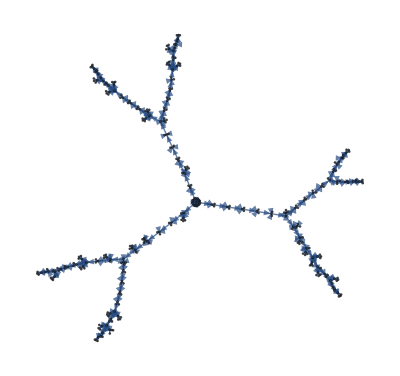

```mathematica
ColorVerdes = { V2, V3, V4}
$Info = False;
$numIter =16;
$FullDFS = True;
$η = 1.5;
Algoritmo[$numIter,Z, {5 , 4}]
Map[{#,colorCaja@cajaNumero[#], valorFuncion@#} &,cajasVerdes[$numIter]]
grafoRecursion
```

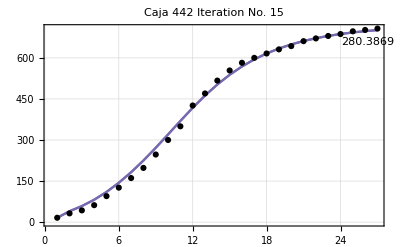

```mathematica
getFigura@cajaNumero@442
```

```mathematica
cajaOptima[12] // valorFuncion
```

447.7247

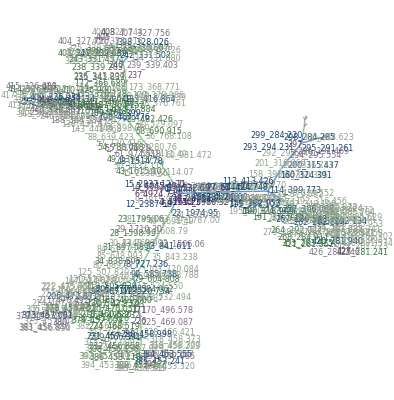

```mathematica
getGrafo[]
```

```mathematica
$Info = False;
$numIter =3;
$FullDFS = True;
Algoritmo[$numIter,Z, {5 , 4}, 0.5]
getGrafo[]
```

```mathematica
guardarSesion[];
EmitSound[Sound[SoundNote[]]]
```

```mathematica
Spea
```